```mathematica
BisRec[f_,a_,b_,xtol_,ytol_,nmax_]:=
Module[{c,fa,fb,fc,p,a1,b1,r},
fa=f[a];
fb=f[b];
c=(a+b)/2.0;
fc=f[c];

If[Abs[a-b]<xtol||Abs[fc]<ytol||nmax≤0, {c,1}];
If[Sign[fa]*Sign[fc]<0,a1=a;,b1=c;
a1=c; b1=b;]
{r,p}=BisRec[f,a,b,xtol,ytol,nmax-1];
{r,p+1}]
```

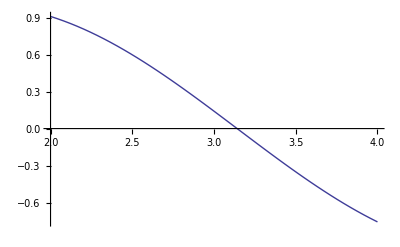

{3.14159,21}

```mathematica
f1[x_]:=Sin[x];Plot[f1[x],{x,2,4}]
Bisection[f1,2,4,10^-6,10^-7,50]
```